```mathematica
Solve[a x^3+b x^2+c x+d==0/.{a->1,b->2,c->3,d->4},x]
```

{{x→1/3 (-2-5^(2/3)/(-7+3 √6)^(1/3)+(5 (-7+3 √6))^(1/3))},{x→-2/3+(5^(2/3) (1+ⅈ √3))/(6 (-7+3 √6)^(1/3))-1/6 (1-ⅈ √3) (5 (-7+3 √6))^(1/3)},{x→-2/3+(5^(2/3) (1-ⅈ √3))/(6 (-7+3 √6)^(1/3))-1/6 (1+ⅈ √3) (5 (-7+3 √6))^(1/3)}}

```mathematica
Solve[x^5-2 x^3+x+5==0,x]
```

{{x→Root[5+#1-2 #1^3+#1^5&,1]},{x→Root[5+#1-2 #1^3+#1^5&,2]},{x→Root[5+#1-2 #1^3+#1^5&,3]},{x→Root[5+#1-2 #1^3+#1^5&,4]},{x→Root[5+#1-2 #1^3+#1^5&,5]}}

```mathematica
NSolve[x^5-2 x^3+x+5==0,x]
```

{{x→-1.65477},{x→-0.527822-1.02701 ⅈ},{x→-0.527822+1.02701 ⅈ},{x→1.35521-0.655415 ⅈ},{x→1.35521+0.655415 ⅈ}}

```mathematica
?#
```

# represents the first argument supplied to a pure function. 
#n represents the n^th argument. 
#name represents the value associated with key "name" in an association in the first argument.

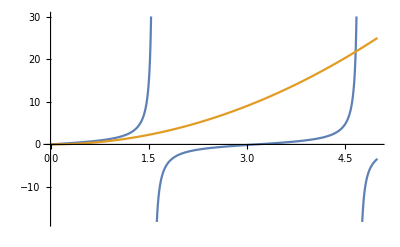

```mathematica
Plot[{Tan[x],x^2},{x,0,5}]
Dynamic[MousePosition["Graphics"]](* 给出鼠标所指位置的坐标 *)
```

```mathematica
NSolve[E^x==x^2,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.703467},{x→1.58805-1.54022 ⅈ}}

```mathematica
FindRoot[E^x==x^2,{x,-1}](* 需要给出一个猜测的解 *)
```

{x→-0.703467}

```mathematica
equation={(1.6 +x) (3 x)^3/((1.4-x) (2.3-x))==1.8 10^-7};
roots=Solve[equation,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-1.6},{x→-0.00118642-0.00206073 ⅈ},{x→-0.00118642+0.00206073 ⅈ},{x→0.00237286}}

```mathematica
p=3 x/.roots[[4]]
```

0.00711858

```mathematica
equations={ka==cH3O cAminus/cHA,kw==cH3O cOH,ca+cb==cHA+cAminus,cb+cH3O==cAminus+cOH};
simplified=Eliminate[equations,{cAminus,cHA,cOH}]
```

cb cH3O^2+cH3O^3+cH3O^2 ka-cH3O kw-ka kw==ca cH3O ka

```mathematica
Clear[roots]
```

```mathematica
roots=Solve[simplified,cH3O]
```

{{cH3O→1/3 (-cb-ka)-(2^(1/3) (-(cb+ka)^2+3 (-ca ka-kw)))/(3 (-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw+√(4 (-(cb+ka)^2+3 (-ca ka-kw))^3+(-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw)^2))^(1/3))+1/(3 2^(1/3))(-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw+√(4 (-(cb+ka)^2+3 (-ca ka-kw))^3+(-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw)^2))^(1/3)},{cH3O→1/3 (-cb-ka)+((1+ⅈ √3) (-(cb+ka)^2+3 (-ca ka-kw)))/(3 2^(2/3) (-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw+√(4 (-(cb+ka)^2+3 (-ca ka-kw))^3+(-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw+√(4 (-(cb+ka)^2+3 (-ca ka-kw))^3+(-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw)^2))^(1/3)},{cH3O→1/3 (-cb-ka)+((1-ⅈ √3) (-(cb+ka)^2+3 (-ca ka-kw)))/(3 2^(2/3) (-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw+√(4 (-(cb+ka)^2+3 (-ca ka-kw))^3+(-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw)^2))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw+√(4 (-(cb+ka)^2+3 (-ca ka-kw))^3+(-2 cb^3-9 ca cb ka-6 cb^2 ka-9 ca ka^2-6 cb ka^2-2 ka^3-9 cb kw+18 ka kw)^2))^(1/3)}}

```mathematica
cH3O/.roots/.{ca->10^-5,cb->0,ka->6.17 10^-10,kw->10^-14}
```

{1.27044×10^-7+7.94093×10^-23 ⅈ,-1.27279×10^-7+7.94093×10^-23 ⅈ,-3.81569×10^-10-1.58819×10^-22 ⅈ}

```mathematica
pH=-Log10[cH3O/.roots/.{ca->10^-5,cb->0,ka->6.17 10^-10,kw->10^-14}]
```

{6.89605-2.71457×10^-16 ⅈ,6.89524-1.36438 ⅈ,9.41843+1.36438 ⅈ}

```mathematica
pH2=Chop[-Log10[cH3O/.roots/.{ca->10^-5,cb->0,ka->6.17 10^-10,kw->10^-14}]]
```

{6.89605,6.89524-1.36438 ⅈ,9.41843+1.36438 ⅈ}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindRoot::argmu: FindRoot called with 1 argument; 2 or more arguments are expected.